```mathematica
ClearAll["Global`*"]
```

```mathematica
resultsPath="/Users/basavyr/Documents/DevWorkspace/GitHub/mathematica-useful-algorithms/Physics/double-beta-pairing-strength/results/";
```

### Experimental data

```mathematica
ydataP={0.36,0.34,0.18,0.38,0.20,0.27,0.27,0.24};
ydataN={0.38,0.36,0.433,0.36,0.245,0.22,0.24,0.26};
xdata={76,82,96,100,116,128,130,150};
xdataL=1/#&@xdata;
expdataP=Table[{xdata[[i]],ydataP[[i]]},{i,1,Length[xdata]}];
expdataN=Table[{xdata[[i]],ydataN[[i]]},{i,1,Length[xdata]}];
```

### Plot style

```mathematica
mystyle = {Frame -> True, Axes -> False, FrameStyle -> Directive[Black, Thick], 
    LabelStyle -> {19, Bold, Black, FontFamily -> "Times"}, AspectRatio -> 0.8, 
    PlotRange->{0,0.5},ImageSize->380};
```

### Model

```mathematica
(*the pairing strength for protons*)
gp[a_,b_,x_]:=b+a*1/x;
(*the pairing strength for protons*)
gn[c_,d_,x_]:=d+c*1/x;
protonParams=Values@FindFit[expdataP,b+a*1/x,{a,b},x];
neutronParams=Values@FindFit[expdataN,d+c*1/x,{c,d},x];
Print[protonParams]
Print[neutronParams]
```

{17.2435,0.114976}

{27.4379,0.0496632}

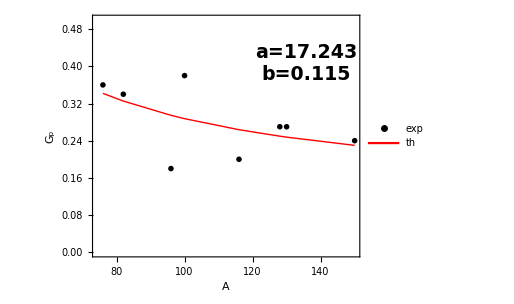

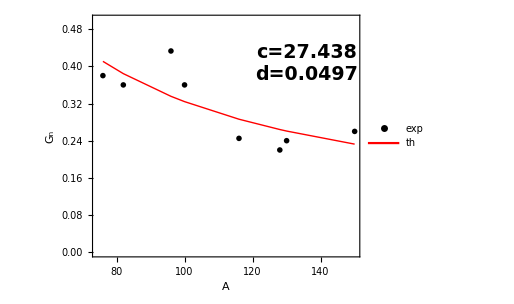

```mathematica
figP=ListPlot[{expdataP,Table[{xdata[[i]],gp[protonParams[[1]],protonParams[[2]],xdata[[i]]]},{i,1,Length[xdata]}]},Evaluate[mystyle],PlotLegends->Placed[{"exp","th"},{0.8,0.2}],Joined->{False, True},PlotMarkers->{{"●",Scaled[0.05]},None},PlotStyle->{{Black},{Red,Thick}},FrameLabel->{"A","G_p"},Epilog->{Inset[Style[StringTemplate["a=``\nb=``"][SetPrecision[protonParams[[1]],5],SetPrecision[protonParams[[2]],3]],19,Bold,Black,FontFamily->"Times"],Scaled[{0.8,0.8}]]}];
figN=ListPlot[{expdataN,Table[{xdata[[i]],gn[neutronParams[[1]],neutronParams[[2]],xdata[[i]]]},{i,1,Length[xdata]}]},Evaluate[mystyle],PlotLegends->Placed[{"exp","th"},{0.2,0.2}],Joined->{False, True},PlotMarkers->{{"●",Scaled[0.05]},None},PlotStyle->{{Black},{Red,Thick}},FrameLabel->{"A","G_n"},Epilog->{Inset[Style[StringTemplate["c=``\nd=``"][SetPrecision[neutronParams[[1]],5],SetPrecision[neutronParams[[2]],3]],19,Bold,Black,FontFamily->"Times"],Scaled[{0.8,0.8}]]}];
Show[figP]
Show[figN]
Export[StringTemplate["``/Gp.pdf"][resultsPath],figP];
Export[StringTemplate["``/Gn.pdf"][resultsPath],figN];
```

## Using the numerical minimization

```mathematica
minP=Values@NMinimize[Sqrt[1/Length[ydataP] Sum[(ydataP[[i]]-gp[a,b,xdata[[i]]])^2/ydataP[[i]],{i,1,Length[ydataP]}]],{a,b}][[2]];
minN=Values@NMinimize[Sqrt[1/Length[ydataN] Sum[(ydataN[[i]]-gn[c,d,xdata[[i]]])^2/ydataN[[i]],{i,1,Length[ydataN]}]],{c,d}][[2]];
Print[minP]
Print[minN]
```

{14.4798,0.127117}

{27.9965,0.0381972}

```mathematica
rms[data_,datath_]:=Sqrt[1/Length[data]*Sum[(data[[i]]-datath[[i]])^2/data[[i]],{i,1,Length[data]}]];
```